```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\work\critical_region\cheby\LPA\v1\nu\mub0Tc\buffer

```mathematica
list0=Flatten[Import["a.dat"]];
list=Flatten[Import["b.dat"]];
```

```mathematica
list1=Rest[list0];
list2=Rest[list];
```

```mathematica
ρmin=0;
ρmax=30000;
c0=1.85*10^6;
fpi=93.5;
cmax=10.^7;
cmin=10.^-2;
```

```mathematica
rhoend=80;
eqn6=Table[Evaluate[(test=SetPrecision[Sum[list1[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,190}]+1/2 First[list1],52])],{ρ,0,rhoend,rhoend/191}];
sigma=Table[√(2 rho),{rho,0,rhoend,rhoend/191}];
```

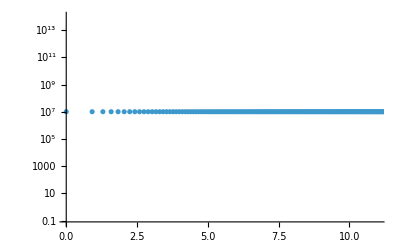

```mathematica
ListPlot[Transpose[{sigma,eqn6-eqn6[[1]]+10^7}],PlotRange->{{0,11},All},ScalingFunctions->{Automatic,"Log"}]
```

```mathematica
rhoend=80;
eqn7=Table[Evaluate[(test=SetPrecision[Sum[list2[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,190}]+1/2 First[list],52])],{ρ,0,rhoend,rhoend/2000}];
sigma=Table[√(2 rho),{rho,0,rhoend,rhoend/2000}];
```

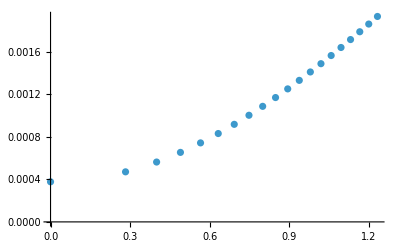

```mathematica
ListPlot[Transpose[{sigma,eqn7}][[1;;20]],PlotRange->All]
```